```mathematica
hedge=Flatten[Import["c:\\book1.txt","Table"],1];
```

```mathematica
Length[hedge]
```

892

```mathematica
g=FinancialData["DAX","1.1.2000"];
```

```mathematica
dax=Transpose[g][[2]][[1;;Length[hedge]]];
```

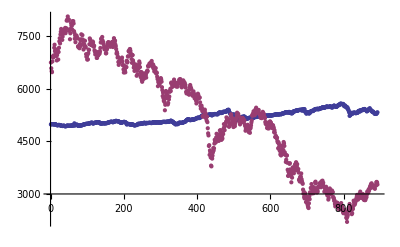

```mathematica
ListPlot[{hedge,dax}]
```

```mathematica
hedge=Log[hedge];dax=Log[dax];
```

```mathematica
hedge=Differences[hedge];
```

```mathematica
dax=Differences[dax];
```

```mathematica
w=Transpose[{hedge,dax}];
```

```mathematica
w=Sort[w,#1[[1]]<#2[[1]]&];
```

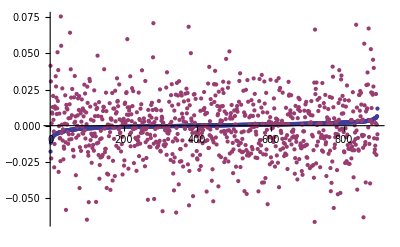

```mathematica
ListPlot[Transpose[w],PlotRange->All]
```

```mathematica
nN=20;wN=Length[hedge];
m0=Min[Transpose[w][[1]]]
Max[Transpose[w][[1]]]
m1=Min[Transpose[w][[2]]]
Max[Transpose[w][[2]]]
f0=(nN-1)/(Max[Transpose[w][[1]]]-m0)
f1=(nN-1)/(Max[Transpose[w][[2]]]-m1)
d=1/wN//N
```

-0.0178719

0.0118256

-0.0665223

0.0755268

639.785

133.757

0.00112233

```mathematica
F[[1,1]]
```

{-0.0665223,-0.0178719,0}

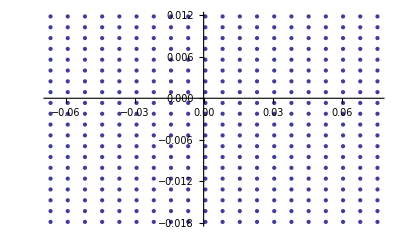

```mathematica
ListPlot[Transpose[Transpose[Q][[1;;2]]]]
```

```mathematica
w[[1]]
```

{0.041439,-0.0178719}

```mathematica
F=Table[{m0+i/f0,m1+j/f1,0},{i,0,nN-1},{j,0,nN-1}];For[i=1,i≤nN,i++,
For[j=1,j≤nN,j++,
For[k=1,k≤wN,k++,
If[w[[k,2]]≤F[[i,j,2]] &&w[[k,1]]≤F[[i,j,1]] ,F[[i,j,3]]+=d;];
]
]];Q=Flatten[F,1];
```

```mathematica
ListPointPlot3D[Q]
```

-Graphics3D-

```mathematica
w=Import["c:\\bivariat.txt","Table"];
```

```mathematica
ListPointPlot3D[w]
```

-Graphics3D-

```mathematica
w[[3]]
```

{-0.017872,-0.063653,0.}

```mathematica
Length[w]
```

10000

```mathematica
w[[1000,2]]
```

0.075527

```mathematica
Table[p,{p,1,9999,1000}]
```

{1,1001,2001,3001,4001,5001,6001,7001,8001,9001}

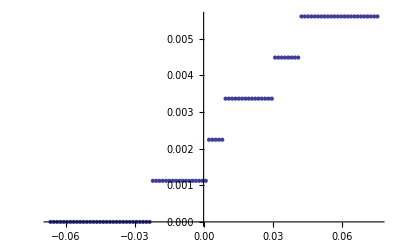

```mathematica
p=3000;ListPlot[{#[[2]],#[[3]]}&/@Select[w,#[[1]]==w[[p,1]]&]]
```

```mathematica
ll={#[[2]],#[[3]]}&/@Select[w,#[[1]]==w[[p,1]]&];
```

```mathematica
ListPlot[ll]
```

-Graphics-

```mathematica
Max[Table[w[[k,3]]-Q[[k,3]],{k,nN^2}]]
```

4.74747×10^-7